```mathematica
(*1q leakage-refocused gates,full 8x8*)ClearAll["Global`*"];

pars1={θ1->0.,θ2->0.,g1->53,g2->74,g3->47};

n1={0,1,0};
n2={0,1,0};
Rot1=RotationMatrix[θ1,Normalize[n1]];
Rot2=RotationMatrix[θ2,Normalize[n2]];

Jidle[gL_,gM_,gS_]:=((gM-gL)^2-(2 gS-gL-gM)^2)/(2 (2 gS-gL-gM))//N;

H1[J12_,J23_]:=(1/2 (g1 KroneckerProduct[PauliMatrix[3],PauliMatrix[0],PauliMatrix[0]]+g2 KroneckerProduct[PauliMatrix[0],PauliMatrix[3],PauliMatrix[0]]+g3 KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[3]])+1/4 Sum[J12 Rot1[[i,j]] KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+J23 Rot2[[i,j]] KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}])/. pars1;

sortedES[H_]:=With[{es=Eigensystem[N[H]]},Transpose[SortBy[Transpose[es],First]]];

(*idle point*)
j12Guess1=Jidle[g1,g2,g3]/. pars1;
j23arr=Range[0,0.3,0.01];
j12arr1=Range[Max[0,j12Guess1-3.],j12Guess1+3.,0.01];

X1=ParallelTable[sortedES[H1[j12,j23]],{j12,j12arr1},{j23,j23arr}];

eigval1=X1[[All,All,1]];
eigval1=eigval1-eigval1[[All,All,1]];
de1=eigval1[[All,All,3]]-eigval1[[All,All,2]];

best1=First@MinimalBy[Flatten[Table[{j12arr1[[i]],j23arr[[j]],de1[[i,j]]},{i,Length[j12arr1]},{j,Length[j23arr]}],1],Abs[Last[#]]&];

j12Idle1=best1[[1]];
j23Idle1=best1[[2]];
{j12Guess1,j12Idle1,j23Idle1,best1[[3]]}
```

{9.81818,9.81818,0.,7.10543×10^-15}

```mathematica
(*fixed Hamiltonian pieces*)HZ=N[H1[0,0]]//Chop;
H12=N[H1[1,0]-H1[0,0]]//Chop;
H23=N[H1[0,1]-H1[0,0]]//Chop;
Hidle=N[HZ+j12Idle1 H12+j23Idle1 H23]//Chop;

Hgate[dJ12_,dJ23_]:=Hidle+dJ12 H12+dJ23 H23;

(*computational basis: |0>is lower branch at J12<J12idle*)
orthogonal2D[{a_,b_}]:={-Conjugate[b],Conjugate[a]};

makeBasis[branch_:2,eps_:0.1]:=Module[{subspaceBasis,perturbedState,coordinates},subspaceBasis=Transpose@sortedES[Hidle][[2,2;;3]];
perturbedState=sortedES[Hidle-eps H12][[2,branch]];
coordinates=Normalize@(ConjugateTranspose[subspaceBasis].perturbedState);
subspaceBasis.Transpose[{coordinates,orthogonal2D[coordinates]}]]


comp=makeBasis[2];
{Chop[ConjugateTranspose[comp].comp],Abs[comp[[7,1]]]^2}

(*If the second number is not close to 1,use:*)
(*comp=makeBasis[3];*)
```

{{{1.,0},{0,1.}},1.}

```mathematica
(*fidelity utilities*)Uproj[dJ12_,dJ23_,t_]:=Module[{U},U=MatrixExp[-I 2 Pi Hgate[dJ12,dJ23] t];
ConjugateTranspose[comp].U.comp];

gateFid[K_,Uid_]:=Module[{d=2},Re[(Tr[ConjugateTranspose[K].K]+Abs[Tr[ConjugateTranspose[Uid].K]]^2)/(d (d+1))]];

infid[K_,Uid_]:=1-gateFid[K,Uid];

leak[K_]:=Module[{d=2},Re[1-Tr[ConjugateTranspose[K].K]/d]];

floor[x_]:=Max[Re[x],10^-16];

eta=((g3-g2)/(g1-g3)/. pars1)//N;

DeltaL=Sqrt[(g1-g2)^2+(2 (g1-g3) (g2-g3)/(g1+g2-2 g3))^2]/. pars1//N;

s=Sqrt[1+eta^2];
NBD=Sqrt[eta^2+2];

ketB={-s,1}/NBD;
ketD={1,s}/NBD;

PB=Outer[Times,ketB,Conjugate[ketB]];
PD=Outer[Times,ketD,Conjugate[ketD]];

{eta,DeltaL}
```

{-4.5,23.1818}

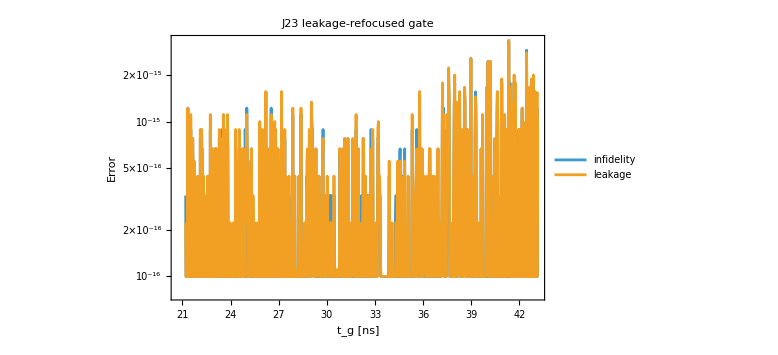

```mathematica
(*J23 leakage-refocused target*)Omega23[dJ23_]:=Sqrt[DeltaL^2+2 DeltaL dJ23/(1+eta^2)+dJ23^2];
t23[dJ23_,n_:1]:=n/Omega23[dJ23];

E23D[dJ23_]:=dJ23/4;
E23B[dJ23_]:=-dJ23 (eta^2+3)/(4 (1+eta^2));
E23L[dJ23_]:=DeltaL+dJ23 (1-eta^2)/(4 (1+eta^2));

Utarget23[dJ23_,n_:1]:=Module[{t,phiB,phiD},t=t23[dJ23,n];
phiD=E23D[dJ23] t;
phiB=((E23B[dJ23]+E23L[dJ23])/2) t+n/2;
Exp[-I 2 Pi phiB] PB+Exp[-I 2 Pi phiD] PD];

metric23[dJ23_,n_:1]:=Module[{t,K,Uid},t=t23[dJ23,n];
K=Uproj[0,dJ23,t];
Uid=Utarget23[dJ23,n];
{1000 t,floor[infid[K,Uid]],floor[leak[K]],dJ23}];

data23=ParallelTable[metric23[dJ23,1],{dJ23,Range[0.1,40,0.05]}];

ListLogPlot[{data23[[All,{1,2}]],data23[[All,{1,3}]]},Joined->True,Frame->True,FrameLabel->{"t_g [ns]","Error"},PlotLegends->{"infidelity","leakage"},PlotLabel->"J23 leakage-refocused gate",ImageSize->Large]
```

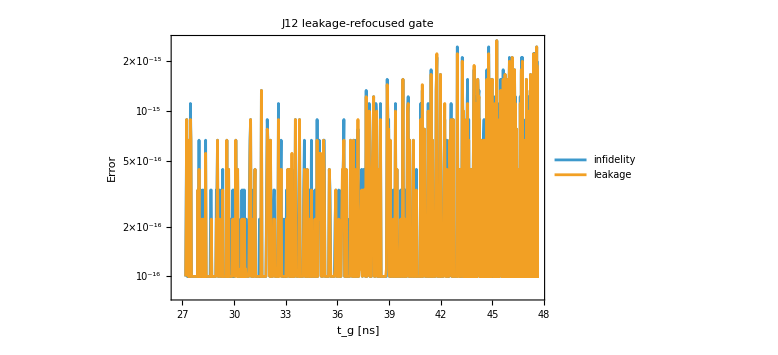

```mathematica
(*J12 leakage-refocused target*)Omega12[dJ12_]:=Sqrt[DeltaL^2-4 eta DeltaL dJ12/(1+eta^2)+dJ12^2];
t12[dJ12_,n_:1]:=n/Omega12[dJ12];

E120[dJ12_]:=dJ12/4;
E121[dJ12_]:=dJ12 (-1/4+eta/(1+eta^2));
E12L[dJ12_]:=DeltaL+dJ12 (-1/4-eta/(1+eta^2));

Utarget12[dJ12_,n_:1]:=Module[{t,phi0,phi1},t=t12[dJ12,n];
phi0=E120[dJ12] t;
phi1=((E121[dJ12]+E12L[dJ12])/2) t+n/2;
DiagonalMatrix[{Exp[-I 2 Pi phi0],Exp[-I 2 Pi phi1]}]];

metric12[dJ12_,n_:1]:=Module[{t,K,Uid},t=t12[dJ12,n];
K=Uproj[dJ12,0,t];
Uid=Utarget12[dJ12,n];
{1000 t,floor[infid[K,Uid]],floor[leak[K]],dJ12}];

data12=ParallelTable[metric12[dJ12,1],{dJ12,Range[-40,-0.1,0.05]}];

ListLogPlot[{data12[[All,{1,2}]],data12[[All,{1,3}]]},Joined->True,Frame->True,FrameLabel->{"t_g [ns]","Error"},PlotLegends->{"infidelity","leakage"},PlotLabel->"J12 leakage-refocused gate",ImageSize->Large]
```

```mathematica
(*Log-binned 1/f noise on a fixed experimental window*)ClearAll[noiseTrace1f,gateDts,sample23,sample12,avg23,avg12,wrapHalf,revPhase,xCoeff23,zCoeff12,findPoint];

noiseTrace1f[amp_,tExpUs_:1.,dtStepUs_:0.0005,fLowHz_:1.,window_:200]:=Module[{nPts,fLowMHz,fNyqMHz,edgesMHz,fMHz,phi,a},nPts=Ceiling[tExpUs/dtStepUs];
fLowMHz=10^-6 fLowHz;
fNyqMHz=1/(2 dtStepUs);
edgesMHz=Exp@Subdivide[Log[fLowMHz],Log[fNyqMHz],window];
fMHz=Sqrt[Most[edgesMHz] Rest[edgesMHz]];
phi=RandomReal[{0,2 Pi},window];
a=amp Sqrt[Log[Rest[edgesMHz]/Most[edgesMHz]]];
Table[Total[a Cos[2 Pi fMHz (k dtStepUs)+phi]],{k,0,nPts-1}]];

gateDts[tg_,dtStepUs_]:=Module[{n=Max[1,Ceiling[tg/dtStepUs]]},Join[ConstantArray[dtStepUs,n-1],{tg-(n-1) dtStepUs}]];

(*One noisy sample:J23 pulse*)
sample23[dJ23_,ampJ12_,ampJ23_,tExpUs_:1.,dtStepUs_:0.0005,window_:200,nRev_:1]:=Module[{tg,dts,n12,n23,U,K,Uid},tg=t23[dJ23,nRev];
If[tg>tExpUs,Return[<|"Infidelity"->Indeterminate,"Leakage"->Indeterminate|>]];
dts=gateDts[tg,dtStepUs];
n12=Take[noiseTrace1f[ampJ12,tExpUs,dtStepUs,1.,window],Length[dts]];
n23=Take[noiseTrace1f[ampJ23,tExpUs,dtStepUs,1.,window],Length[dts]];
U=Fold[Dot,IdentityMatrix[Length[Hidle]],Reverse@Table[MatrixExp[-I 2 Pi dts[[k]] (Hidle+j12Idle1 n12[[k]] H12+dJ23 (1+n23[[k]]) H23)],{k,Length[dts]}]];
K=ConjugateTranspose[comp].U.comp;
Uid=Utarget23[dJ23,nRev];
<|"Infidelity"->1-gateFid[K,Uid],"Leakage"->leak[K]|>];

(*One noisy sample:J12 pulse*)
sample12[dJ12_,ampJ12_,tExpUs_:1.,dtStepUs_:0.0005,window_:200,nRev_:1]:=Module[{tg,dts,n12,U,K,Uid},tg=t12[dJ12,nRev];
If[tg>tExpUs,Return[<|"Infidelity"->Indeterminate,"Leakage"->Indeterminate|>]];
dts=gateDts[tg,dtStepUs];
n12=Take[noiseTrace1f[ampJ12,tExpUs,dtStepUs,1.,window],Length[dts]];
U=Fold[Dot,IdentityMatrix[Length[Hidle]],Reverse@Table[MatrixExp[-I 2 Pi dts[[k]] (Hidle+dJ12 H12+(j12Idle1+dJ12) n12[[k]] H12)],{k,Length[dts]}]];
K=ConjugateTranspose[comp].U.comp;
Uid=Utarget12[dJ12,nRev];
<|"Infidelity"->1-gateFid[K,Uid],"Leakage"->leak[K]|>];

avg23[dJ23_,ampJ12_,ampJ23_,tExpUs_:1.,dtStepUs_:0.0005,window_:200,nSamples_:200,nRev_:1]:=Module[{s},s=Table[sample23[dJ23,ampJ12,ampJ23,tExpUs,dtStepUs,window,nRev],{nSamples}];
<|"Infidelity"->Mean[s[[All,"Infidelity"]]],"Leakage"->Mean[s[[All,"Leakage"]]]|>];

avg12[dJ12_,ampJ12_,tExpUs_:1.,dtStepUs_:0.0005,window_:200,nSamples_:200,nRev_:1]:=Module[{s},s=Table[sample12[dJ12,ampJ12,tExpUs,dtStepUs,window,nRev],{nSamples}];
<|"Infidelity"->Mean[s[[All,"Infidelity"]]],"Leakage"->Mean[s[[All,"Leakage"]]]|>];

(*noise parameters*)
ampJ12=2.5*10^-4;
ampJ23=1.3*10^-3;

tExpUs=1.;
dtStepUs=0.0005;   (*0.5 ns*)
window=200;
nSamples=200;

nRev23=1;
nRev12=1;

(*pulse-amplitude grids in MHz*)
dJ23Vals=Range[0.5,40,0.5];

(*impose physical J12=J12idle+DeltaJ12>=0*)
dJ12Min=-j12Idle1+0.05;
dJ12Max=-0.5;
dJ12Vals=If[dJ12Min<dJ12Max,Range[dJ12Min,dJ12Max,0.5],{}];

(*noisy data;first coordinate stays in ns for plotting*)
data23Noise=ParallelTable[With[{m=avg23[dJ23,ampJ12,ampJ23,tExpUs,dtStepUs,window,nSamples,nRev23]},{1000 t23[dJ23,nRev23],m["Infidelity"],m["Leakage"],dJ23}],{dJ23,dJ23Vals}];

data12Noise=ParallelTable[With[{m=avg12[dJ12,ampJ12,tExpUs,dtStepUs,window,nSamples,nRev12]},{1000 t12[dJ12,nRev12],m["Infidelity"],m["Leakage"],dJ12}],{dJ12,dJ12Vals}];

(*X-90/Z-90 points from exact analytic revival phases*)
targetM90=-1/8;
nx23=2 Sqrt[1+eta^2]/(eta^2+2);

wrapHalf[x_]:=Mod[x+1/4,1/2]-1/4;

revPhase[dJ_,t_,n_]:=((dJ-DeltaL)/2) t[dJ,n]-n/2;

xCoeff23[dJ_,n_]:=nx23 revPhase[dJ,t23,n]/2;
zCoeff12[dJ_,n_]:=revPhase[dJ,t12,n]/2;

findPoint[coeff_,t_,grid_,n_,avg_]:=Module[{seed,shift,dJ,m},seed=First@MinimalBy[grid,Abs@wrapHalf[coeff[#,n]-targetM90]&];
shift=Round[2 (targetM90-coeff[seed,n])]/2;
dJ=u/. FindRoot[coeff[u,n]+shift==targetM90,{u,seed}];
m=avg[dJ];
{1000 t[dJ,n],m["Infidelity"],m["Leakage"],dJ,wrapHalf[coeff[dJ,n]]}];

xm90=findPoint[xCoeff23,t23,Range[0.5,40,0.01],nRev23,avg23[#,ampJ12,ampJ23,tExpUs,dtStepUs,window,nSamples,nRev23]&];

zm90=findPoint[zCoeff12,t12,Range[-j12Idle1+0.05,-0.5,0.01],nRev12,avg12[#,ampJ12,tExpUs,dtStepUs,window,nSamples,nRev12]&];

{"X-90 {tg ns, infid, leakage, dJ23, coeff}"->xm90,"Z-90 {tg ns, infid, leakage, dJ12, coeff}"->zm90}
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{X-90 {tg ns, infid, leakage, dJ23, coeff}→{33.9621,0.0000217919,3.44436×10^-6,17.0963,-0.125},Z-90 {tg ns, infid, leakage, dJ12, coeff}→{47.5094,4.95755×10^-9,4.66603×10^-10,-8.39086,-0.125}}

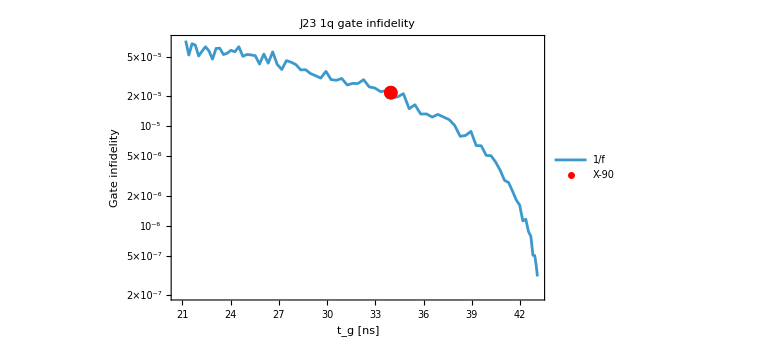
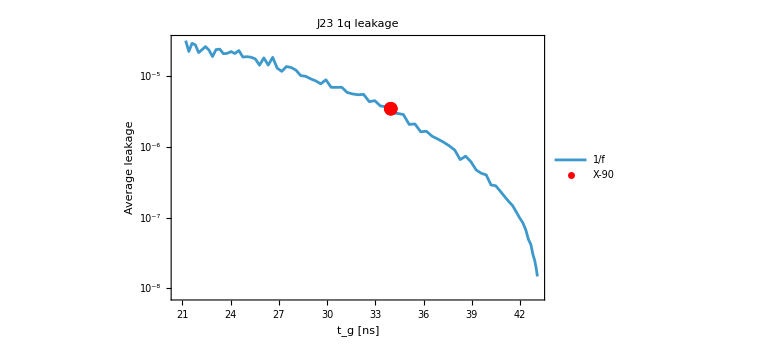
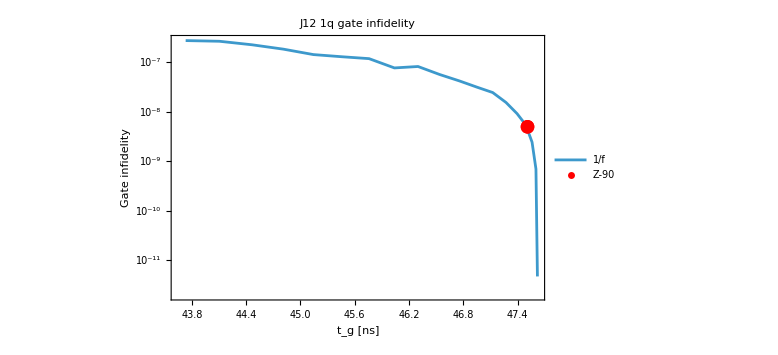
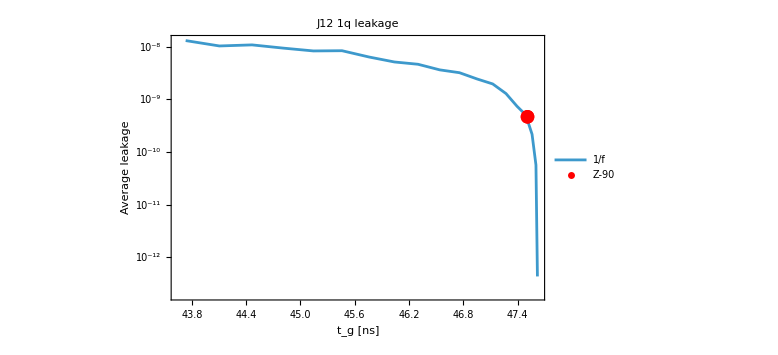

```mathematica
p23Infid=ListLogPlot[{data23Noise[[All,{1,2}]],{xm90[[{1,2}]]}},Frame->True,Joined->{True,False},FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"J23 1q gate infidelity",PlotLegends->{"1/f","X-90"},PlotMarkers->{None,{"●",14}},PlotStyle->{Automatic,Red},ImageSize->Large,PlotRange->All];

p23Leak=ListLogPlot[{data23Noise[[All,{1,3}]],{xm90[[{1,3}]]}},Frame->True,Joined->{True,False},FrameLabel->{"t_g [ns]","Average leakage"},PlotLabel->"J23 1q leakage",PlotLegends->{"1/f","X-90"},PlotMarkers->{None,{"●",14}},PlotStyle->{Automatic,Red},ImageSize->Large,PlotRange->All];

p12Infid=ListLogPlot[{data12Noise[[All,{1,2}]],{zm90[[{1,2}]]}},Frame->True,Joined->{True,False},FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"J12 1q gate infidelity",PlotLegends->{"1/f","Z-90"},PlotMarkers->{None,{"●",14}},PlotStyle->{Automatic,Red},ImageSize->Large,PlotRange->All];

p12Leak=ListLogPlot[{data12Noise[[All,{1,3}]],{zm90[[{1,3}]]}},Frame->True,Joined->{True,False},FrameLabel->{"t_g [ns]","Average leakage"},PlotLabel->"J12 1q leakage",PlotLegends->{"1/f","Z-90"},PlotMarkers->{None,{"●",14}},PlotStyle->{Automatic,Red},ImageSize->Large,PlotRange->All];

{p23Infid,p23Leak,p12Infid,p12Leak}
```

```mathematica
Export["/Users/tivakhtel/SOSO-qubit/tess_code/1q_revival_noise_panel.json",<|"j23_scan"->(AssociationThread[{"tg_ns","infidelity","leakage","dJ_MHz"},#]&/@data23Noise),"j12_scan"->(AssociationThread[{"tg_ns","infidelity","leakage","dJ_MHz"},#]&/@data12Noise),"x90"->Join[<|"label"->"X-90"|>,AssociationThread[{"tg_ns","infidelity","leakage","dJ_MHz","coeff"},xm90]],"z90"->Join[<|"label"->"Z-90"|>,AssociationThread[{"tg_ns","infidelity","leakage","dJ_MHz","coeff"},zm90]]|>,"JSON"]
```

/Users/tivakhtel/SOSO-qubit/tess_code/1q_revival_noise_panel.json